```mathematica
chain={{3,3,3}, {3,3,4}};
```

```mathematica
dimMap={1->{1,0,0},2->{0,1,0},3->{0,0, 1}}
```

{1→{1,0,0},2→{0,1,0},3→{0,0,1}}

```mathematica
addPoint[chain_,box_]:=Module[{lastLink, newLink},
lastLink=Last[chain];
newLink=lastLink+Sign[Random[]-0.5]*(chooseDimension[]/.dimMap);
If[newLink[[1]]≤box && newLink[[1]]≥1 && newLink[[2]]≤box && newLink[[2]]≥1 && newLink[[3]]≤box && newLink[[3]]≥1 ,
If[MemberQ[chain, newLink], chain, Append[chain, newLink]], chain]]
```

```mathematica
(* For some reason this isn't working now *)
generateChain[chain_, box_, iterations_]:=Module[{newChain},
newChain = chain;
For[i=1, i<iterations,i++,
newChain=addPoint[newChain, box];];
newChain
]
```

```mathematica
chainLengths={};
For[j=1,j<5000,
chainLengths=Append[chainLengths,Length[generateChain[{{3,3,3}, {3,3,4}}, 5, 500]]];
j++]
```

```mathematica
countItems[list_, item_]:=Length[Select[list, #== item &]]
```

```mathematica
data={#, countItems[Floor[#/2]&/@chainLengths, #]}&/@Range[63];
```

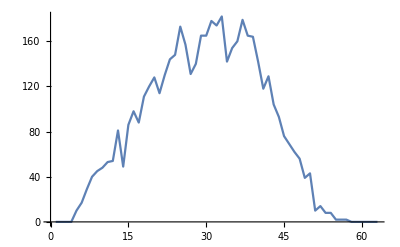

```mathematica
(* Iteresting shape - doesn't look Gaussian or Poisson.  One slope going up, another one going down *)
ListPlot[data, Joined->True]
```

```mathematica
Graphics3D[{Sphere[#, 0.2]&/@chain, Line[{chain[[#]], chain[[#+1]]}]&/@Range[Length[chain]-1]}]
```

-Graphics3D-